## Zeros of GL coefficients in isotropic systems

```mathematica
S[m_]:=((2^m-1)Zeta[m])/(2π )^(m-1)
```

### s-wave Zeeman & s-wave SC (same for d-wave SC)

```mathematica
αseriesSS[maxn_,T_,hoT_]:=Log[T]+Sum[(-1)^(m-1)S[2m+1] hoT^(2m),{m,maxn}]
βseriesSS[maxn_,hoT_]:=Sum[(-1)^(m-1)Binomial[2m,2]S[2m+1] hoT^(2m-2),{m,maxn}]
```

N_max = 2

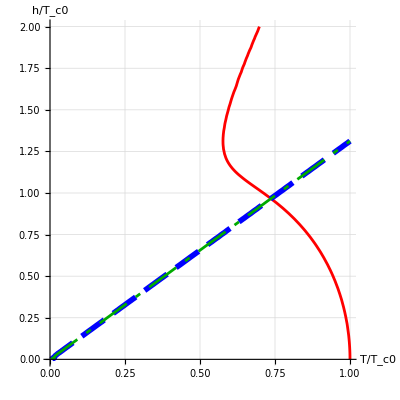

N_max = 100

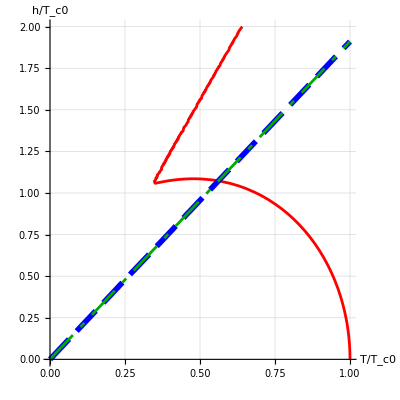

```mathematica
Module[{plt},
Do[
Print["N_max = ",maxn];
plt=ContourPlot[
{αseriesSS[maxn,T,h/T]==0,βseriesSS[maxn,h/T]==0,βseriesSS[maxn,h/T]==0},{T,0,1},{h,0,2},
ContourStyle->{Red,{Blue,Thickness[0.01],Dashing[{0.05,0.02}]},{Darker[Green],Dashing[{0.06,0.02,0.01,0.02}]}},
TicksStyle->20,GridLines->Automatic,
Frame->False,Axes->True,
AxesLabel->{Text[Style["T/T_c0",FontFamily->"Times",Italic,FontSize->30]],Text[Style["h/T_c0",FontFamily->"Times",Italic,FontSize->30]]}
];
Print[plt],
{maxn,{2,100}}
]
]
```

### d-wave Zeeman & s-wave SC

```mathematica
αseriesDS[maxn_,T_,hoT_]:=Log[T]+Sum[(-1)^(m-1)((2m)!)/(2^m(m!)^2)S[2m+1] hoT^(2m),{m,maxn}]
βseriesDS[maxn_,hoT_]:=Sum[(-1)^(m-1)((2m)!)/(2^m(m!)^2)m^2 S[2m+1] hoT^(2m-2),{m,maxn}]
κseriesDS[maxn_,T_,hoT_,EF_]:=Sum[(-1)^(m-1)((2m)!)/(2^m(m!)^2)m(m-((T hoT)/EF)^2)S[2m+1] hoT^(2m-2),{m,maxn}]
```

E_F/T_c0=1, N_max=100

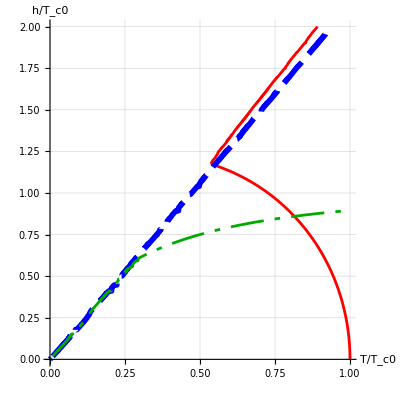

E_F/T_c0=∞, N_max=100

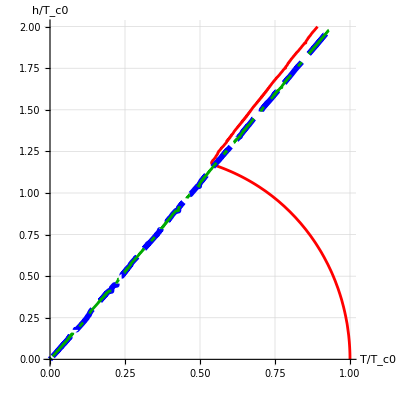

```mathematica
Module[{plt},
Do[
Print["E_F/T_c0=",EF,", N_max=",maxn];
plt=ContourPlot[
{αseriesDS[maxn,T,h/T]==0,βseriesDS[maxn,h/T]==0,κseriesDS[maxn,T,h/T,EF]==0},{T,0,1},{h,0,2},
ContourStyle->{Red,{Blue,Thickness[0.01],Dashing[{0.05,0.02}]},{Darker[Green],Dashing[{0.06,0.02,0.01,0.02}]}},
TicksStyle->20,GridLines->Automatic,
Frame->False,Axes->True,
AxesLabel->{Text[Style["T/T_c0",FontFamily->"Times",Italic,FontSize->30]],Text[Style["h/T_c0",FontFamily->"Times",Italic,FontSize->30]]}
];
Print[plt],
{EF,{1,Infinity}},{maxn,{100}}
]
]
```

### d-wave Zeeman & d-wave SC

```mathematica
αseriesDD[maxn_,T_,hoT_]:=Log[T]+Sum[(-1)^(m-1)((2m+2)!)/(2^(m+1)((m+1)!)^2)S[2m+1] hoT^(2m),{m,maxn}]
βseriesDD[maxn_,hoT_]:=Sum[(-1)^(m-1)((2m)!)/(2^m(m!)^2)m (4 m^2-1)/(m+1)S[2m+1] hoT^(2m-2),{m,maxn}]
κseriesDD[maxn_,T_,hoT_,EF_]:=Sum[(-1)^(m-1)((2m)!)/(2^m(m!)^2)m((2m-1)-(2m+1)/(m+1)((T hoT)/EF)^2)S[2m+1] hoT^(2m-2),{m,maxn}]
```

E_F/T_c0=1, N_max=100

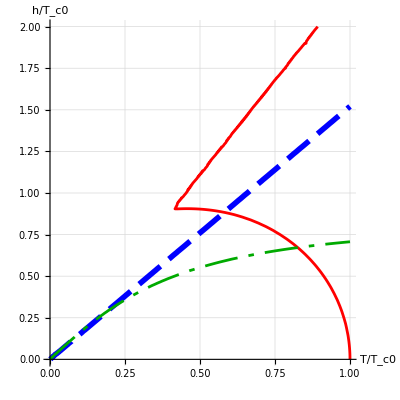

E_F/T_c0=∞, N_max=100

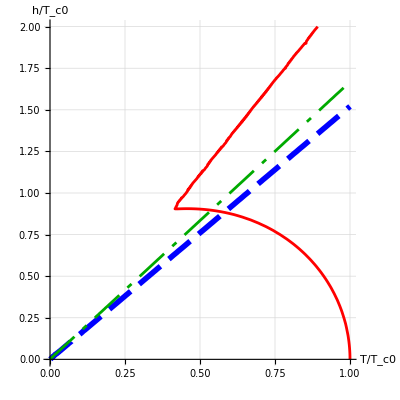

```mathematica
Module[{plt},
Do[
Print["E_F/T_c0=",EF,", N_max=",maxn];
plt=ContourPlot[
{αseriesDD[maxn,T,h/T]==0,βseriesDD[maxn,h/T]==0,κseriesDD[maxn,T,h/T,EF]==0},{T,0,1},{h,0,2},
ContourStyle->{Red,{Blue,Thickness[0.01],Dashing[{0.05,0.02}]},{Darker[Green],Dashing[{0.06,0.02,0.01,0.02}]}},
TicksStyle->20,GridLines->Automatic,
Frame->False,Axes->True,
AxesLabel->{Text[Style["T/T_c0",FontFamily->"Times",Italic,FontSize->30]],Text[Style["h/T_c0",FontFamily->"Times",Italic,FontSize->30]]}
];
Print[plt],
{EF,{1,Infinity}},{maxn,{100}}
]
]
```